# Receiver operating characteristics for AWGN channels

This notebook contains code for generating receiver operating characteristics for energy detectors operating on AWGN channels. The approximation error is also plotted.

### Copyright notice

Copyright (C) 2013 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

01/05/2013
1.0

### Changelog

Version 1.0: First working version.

## Set up

Clear all symbol values and load function definitions:

```mathematica
Unprotect["Global`*"];
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<definitions.m
```

## Variables

Here, we define the parameters to be used:

```mathematica
probabilityOfFalseAlarmRange=Range[0,1,0.01];
testVectors={
(* diversityType, channelType, M, γ (dB) *)
{"ND","AWGN",176,-8},
{"ND","AWGN",708,-10},
{"ND","AWGN",2828,-12}
};
```

Set this to True, if you want to export graphics in EPS format:

```mathematica
exportEPS=True;
```

## Calculations

Calculate the detection probabilities and approximation errors:

```mathematica
{diversityType,channelType,M,γdb}=Transpose[testVectors];
methods={"ExactNumerical","ApproximateNumerical"};
```

```mathematica
rocData=ParallelTable[{ProbabilityOfFalseAlarm[M[[t]],λ[M[[t]],Pf,DiversityType->diversityType[[t]],Method->"Exact"],DiversityType->diversityType[[t]],Method->method],ProbabilityOfDetection[M[[t]],10^(γdb[[t]]/10),λ[M[[t]],Pf,DiversityType->diversityType[[t]],Method->"Exact"],ChannelType->channelType[[t]],DiversityType->diversityType[[t]],Method->method]},{t,Length[testVectors]},{method,methods},{Pf,probabilityOfFalseAlarmRange},DistributedContexts->All];
```

```mathematica
rocPlotData=Flatten[ParallelTable[{rocData[[t,1]],rocData[[t,2]][[1;;;;Floor[Length[probabilityOfFalseAlarmRange]/10]]]},{t,Length[testVectors]},DistributedContexts->All],1];
```

```mathematica
errorData=ParallelTable[Transpose[{probabilityOfFalseAlarmRange,Sqrt[(rocData[[i,1]][[All,1]]-rocData[[i,2]][[All,1]])^2+(rocData[[i,1]][[All,2]]-rocData[[i,2]][[All,2]])^2]}],{i,Length[testVectors]},DistributedContexts->All];
```

```mathematica
errorBounds=ParallelTable[{Pf,√2 ApproximationError[M[[t]],10^(γdb[[t]]/10),ChannelType->channelType[[t]],DiversityType->diversityType[[t]],Method->Last[methods]]},{t,Length[testVectors]},{Pf,probabilityOfFalseAlarmRange},DistributedContexts->All];
```

## Results

### Receiver operating characteristics

```mathematica
exportFileName=FileBaseName[NotebookFileName[]]<>".eps";
```

```mathematica
frameLabel=If[exportEPS,{"X","Y"},{"P_f","P_d"}];
```

```mathematica
plotStyles=Black;
```

```mathematica
plotMarkerSize=If[exportEPS,PlotMarkerSize,DisplayPlotMarkerSize];
```

```mathematica
plotMarkers=Flatten[Table[{NoMarker,Markers[Black,plotMarkerSize][[i]]},{i,Length[testVectors]}]];
```

```mathematica
joined=Flatten[Table[{True,False},{Length[testVectors]}]];
```

```mathematica
legendTextSpace=If[exportEPS,4,4];
```

```mathematica
legendSize=If[exportEPS,{0.75,1},{0.5,0.8}];
```

```mathematica
legendPosition=If[exportEPS,{0.91,-0.42},{1,-0.35}];
```

```mathematica
plotLegend=If[exportEPS,CharacterRange["A","W"][[1;;Length[testVectors]Length[methods]]],Flatten[Table[(((Flatten[{#}][[1]])&[t[[1]]])<>#)&/@{", exact",", approximate"},{t,testVectors}]]];
```

```mathematica
plotLegends=Placed[Grid[Transpose[{Markers[Black,plotMarkerSize][[1;;Length[testVectors]]],If[exportEPS,StringJoin/@CharacterRange["A","W"][[1;;Length[testVectors]]],("N="<>ToString[#[[3]]]<>", γ="<>ToString[#[[4]]]<>"dB")&/@testVectors]}],Alignment->Left],If[exportEPS,{0.7,0.15},{1.02,0.5}]];
```

```mathematica
imageSize=If[exportEPS,IEEETCOM,DisplayImageSize];
```

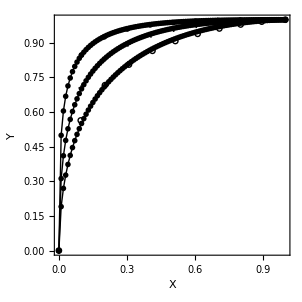

```mathematica
ListPlot[rocPlotData,Joined->joined,PlotStyle->plotStyles,Frame->True,FrameLabel->frameLabel,ImageSize->imageSize,PlotMarkers->plotMarkers,Axes->False,PlotRange->{All,{0,1}},AspectRatio->1,PlotLegends->plotLegends]
If[exportEPS,Export[FileNameJoin[{exportDirectory,exportFileName}],%]];
```

### Approximation error

```mathematica
exportFileName=FileBaseName[NotebookFileName[]]<>"_error.eps";
```

```mathematica
frameLabel=If[exportEPS,{"X","Y"},{"P_f","|ϵ_ROC|"}];
```

```mathematica
basePlotStyles=ThesisFaintColours;
```

```mathematica
plotStyles=Flatten[{Table[Directive[Black],{Length[testVectors]}],Table[Directive[Black],{Length[testVectors]}],Table[Directive[Black,x],{x,{Dashed,Dotted,DotDashed}}][[1;;Length[Tally[errorBounds][[All,1]]]]]}];
```

```mathematica
plotMarkerSize=If[exportEPS,PlotMarkerSize,DisplayPlotMarkerSize];
```

```mathematica
plotMarkers=Flatten[{Table[NoMarker,{i,Length[testVectors]}],Table[Markers[Black,plotMarkerSize][[i]],{i,Length[testVectors]}],NoMarker}];
```

```mathematica
joined=Flatten[{Table[True,{i,Length[testVectors]}],Table[False,{i,Length[testVectors]}],True}];
```

```mathematica
plotLegends=Placed[Grid[Transpose[{Markers[Black,plotMarkerSize][[1;;Length[testVectors]]],If[exportEPS,StringJoin/@CharacterRange["A","W"][[1;;Length[testVectors]]],("N="<>ToString[#[[3]]]<>", γ="<>ToString[#[[4]]]<>"dB")&/@testVectors]}],Alignment->Left],If[exportEPS,{0.1,0.85},{1.02,0.5}]];
```

```mathematica
imageSize=If[exportEPS,IEEETCOM,DisplayImageSize];
```

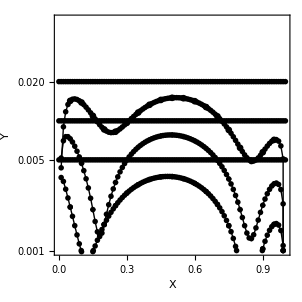

```mathematica
ListLogPlot[Flatten[{errorData,errorData[[All,1;; ;;5]],Tally[errorBounds][[All,1]]},1],Joined->joined,PlotStyle->plotStyles,PlotMarkers->plotMarkers,Frame->True,FrameLabel->frameLabel,ImageSize->imageSize,PlotLegends->plotLegends,PlotRange->{All,{10^-3,3 Max[Transpose[Tally[errorBounds][[All,1]][[1]]][[2]]]}},AspectRatio->1]
If[exportEPS,Export[FileNameJoin[{exportDirectory,exportFileName}],%]];
```